```mathematica
(****
TEMPLATE FOR ITERATIVE OPTIMIZATION ALGORITHMS
Zicheng Gao
 ****)
```

```mathematica
(*** Iteration Settings ***)
InitIterationSettings[]:=(
(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;
doPoint=True;
doGraph=False;
doEPlot=True;
showAll=False;

(** Adaptivity **)
BoostRatio=1.05;
RefineRatio=0.8;
MaxCorrections=50;
ErrorRatio=1.0;

(* Acceleration *)
AccelBoost=1.;
AccelRefine=1.;
AccelAmt=0.00;

ContourResolution=20;
showMistakes=False;
fps=0;

(* Tracker values *)
historyAmt=50;
RefreshInterval=50;
);
InitIterationSettings[];
```

```mathematica
InitFunctionData[steepness_,sharpness_,paramVariance_,manualTrueParams_, noiseDistribution_,seed_,forceData_]:=(
Clear[eFunc,params];
ParamVariance=paramVariance;

SetupSampling[]:=(
SamplingSet=N@Range@DataLength/N@SamplingRate;
Default[DataWith,2]=SamplingSet;
DataWith[p_,range_.]:=(Fitfunction@@Prepend[p,#])&/@range;
);

(*If we are forcing data, use data, otherwise generate data*)
If[Length[forceData]>0,
Data=forceData;
DataLength=Length[Data];
SetupSampling[];
(* Else *),
SetupSampling[];
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-paramVariance,paramVariance},varamt]];
(* Data Generation *)
SeedRandom[seed];
NoiselessData=DataWith@TrueParams;
AddNoise=(#+RandomVariate[noiseDistribution])&;
Data=AddNoise/@NoiselessData;
];

If[normalizeData,
DataN=Norm@Data;
Data=Normalize@Data;
G[]:=DataN Normalize@(DataWith@iterParams);
,
DataN=1;
G[]:=DataWith@iterParams;
];
params=Table[Unique["p"],{varamt}];paramh=Hold@@params;

(*Data is already normalized...?*)
Angdif[v_,w_]:=(If[Norm@v==0||Norm@w==0,Return@0];N@v.w/(Sqrt[N@v.v]*Sqrt[N@w.w]));
Κ=steepness;Q=sharpness;
AngMap[x_]:=Κ((x-1)^2+1-Exp[-Q(x-1)^2])/5;

SOF=paramh/._[vars__]:>Function[{vars},AngMap@N[Angdif[(Normalize@DataWith@{vars}),Data]]];
NLS=paramh/._[vars__]:>Function[{vars},Mean@((Normalize@DataWith@{vars}-Data)^2)];
HNLS=paramh/._[vars__]:>Function[{vars},Mean@((DataWith@{vars}-Data)^2)];
LS=paramh/._[vars__]:>Function[{vars},Mean@((DataWith@{vars}-DataN Data)^2)];

(*Normalized Least Squares*)
);

FindError[]:=(AError=(Total[(G[]-DataN Data)^2]/(DataLength-varamt))^0.5;);

(*** Global Iteration Reset / Initialize ***)
InitIterationData[factorx_,manualParams_]:=(
totalIter=0;
factor=factorx;

Corrections=0;
ConsecCorrections=0;

(*History*)
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams={iterParams};
err=eFunc@@iterParams;
prevErr=err+1.;

debugErr={err};
doPerturb=False;
FindError[];
);
LinePlot[points_, size_,amount_]:=Show[ListPointPlot3D[{If[amount>0&&size>amount,points[[-amount;;-1]],points]},PlotRange->All,ImageSize->Medium],Graphics3D@Line@If[amount>0&&size>amount,points[[-amount;;-1]],points]];
Default[RefreshSPlot,1]="Speed";
RefreshSPlot[goal_.]:=Module[{dims=Take[#,2]&/@debugParams},
If[varamt≠2,Return[False]];
sqcontour=(1-(#-1)^2)^0.5&;
ChopRange[min_,max_,res_,func_]:=func@(Range[0,1,1/res])*(max-min)+min;
SPlot=Evaluate@ContourPlot[
eFunc@@{x,y,0},
Evaluate@({x,-1.+Min@#,1.+Max@#}&@(First/@dims)),
Evaluate@({y,-1.+Min@#,1.+Max@#}&@(Last/@dims)),
Contours->Function[{min,max},ChopRange[max,min,ContourResolution,sqcontour]],
PlotLegends->Automatic,PerformanceGoal->goal,ImageSize->300,PlotRange->All];];
SLinePlot[points_,size_,amount_]:=Show[SPlot,Graphics@Line@(If[amount>0&&size>amount,points[[-amount;;-1]],points])];

Visualize[]:=
Dynamic@Grid[{
{"Data vs Function","Parameter Space","Error over iterations"},
{ListPlot[{G[],DataN Data},Joined->True,ImageSize->Medium,PlotLegends->None],
If[doPoint,Which[
varamt==3,LinePlot[debugParams,totalIter,historyAmt],
varamt==2,SLinePlot[debugParams,totalIter,historyAmt],
True,"Incorrect dimensionality"],"Disabled"],
If[doEPlot,ListLogPlot[debugErr,ImageSize->Medium,PlotRange->All],"Disabled"]},
{"Parameters","Iterations, corrections, α, β, LSTolerance, factor","Deviation, Objective"},
{If[showAll||varamt<5,Column[{iterParams}],"Displaying parameters would take too much space."],
Column[{{totalIter,Corrections},{ProgressIndicator[ConsecCorrections/MaxCorrections],α,β},{LSTol,factor}}],
{AError,prevErr}}
},Frame->All,ItemSize->30];

AddToHistory[]:=(debugParams=Append[debugParams,iterParams];debugErr=Append[debugErr,err];);
ToSpacedString=Function[str,StringDrop[StringJoin@@((ToString[#]<>" ")&/@str),-1]];

(*Golden Ratio Search*)
Default[GoldenRatioSearch,8]=False; (* Verbose *)
Default[GoldenRatioSearch,9]=0; (* Constrain iterations *)
GoldenRatioSearch[coeff_,init_,d_,surface_,tolerance_,min_,LSTemp_,verbose_.,max_.]:=Module[{
gr=N@GoldenRatio,f=coeff,l=coeff-LSTemp,h=coeff+N@GoldenRatio*LSTemp,g=coeff+N@GoldenRatio*LSTemp-LSTemp,
e=surface@@(init+#*d)&,i=0,eg,ef,eh,el,
goLeft,goRight,trials=If[verbose,{}]},
While[Abs[f-g]>tolerance&&(max==0||(max≠0&&i++<max)),
If[verbose,trials=Append[trials,{l,f,g,h}]];
eg=e@g;ef=e@f;eh=e@h;el=e@l;
If[eh<ef&&eh<eg,h+=(h-l)*gr;,(* Imbalanced *)
If[el<ef&&el<eg,l=l-gr (h-l),
If[ef<eg,h=g,l=f](* No Problems *)];];
f=h-(h-l)/gr;g=l+(h-l)/gr;
];
If[verbose,trials=Append[trials,{l,f,g,h}];Return@trials,Return@f];
];

RefineFactor[f_]:=(f*=RefineRatio^AccelRefine;ConsecCorrections++;Corrections++;AccelRefine+=AccelAmt;AccelBoost=1.;Return@f);
BoostFactor[f_,ceil_]:=(ConsecCorrections=0;f*=BoostRatio^AccelBoost;AccelRefine=1.;If[f>ceil,Return@ceil]AccelBoost+=AccelAmt;Return@f);

Default[RandomDirection]=1.;
RandomDirection[m_.]:=Module[
{v=ConstantArray[0,varamt]},
While[Norm@v==0,v=Normalize[RandomReal[1.,varamt]]];
Return[v*m];
];
RandomPerp[to_]:=Module[
{v=ConstantArray[0,varamt],m=Norm@to},
While[Norm@v==0,v=RandomDirection[m];v=v-to*v.Normalize@to];
Return[Normalize@v*m];
];

PolyN[degree_]:=Total@(Array[Slot,degree+1,2]*Flatten@MapIndexed[#1^(#2-1)&,Slot/@ConstantArray[1,degree+1]]);

Default[GridSearch,5]={0,0};
Default[IterGridSearch,7]={0,0};
GridSearch[s_,size_,depth_,carry_,offset_.]:=Module[{i},
i=#+offset&/@Flatten[Table@@Prepend[{#,-size,size,2.size/depth}&/@params,params],1];
Return[Drop[#,-1]&/@Take[SortBy[Append[#,s@@#]&/@i,Last],carry]]
];
(*
s: search surface;
size: numeric range of initial region;
depth: how many samples along any one dimension to make;
carry: number of top candidates to carry into next iteration;
factor: successive iterations' size is actually 'intended size' * factor;
n: iteration number;
offset: initial center of region;
*)
IterGridSearch[s_,size_,depth_,carry_,factor_,n_,offset_.]:=Module[{i={{0.,0.}},j=n-1},
If[n==0,Print["Invalid Iteration Count. Use n ≥ 1."];Return@i];
i=GridSearch[s,size,depth,carry,offset];
While[j>0,i=First@GridSearch[s,factor*2*size/depth,depth,carry,#]&/@i;j--;];
Return@i];

(* Nelder Mead, iterates iterParams *)
Iterate[n_,tolerance_,factor_,temp_,prate_,pmax_]:=Module[{
i=0,
ω=factor,
heat=temp,
λ={}(* Simplex Points *),
Λ={}(* Centroid *),
e=eFunc@@#&
},(
While[(i<n &&(NoErr||(AError>tolerance))),
If[doPoint&&varamt==2&&Mod[totalIter,RefreshInterval]==0,RefreshSPlot["Speed"];];

err=e@iterParams;

If[eFunc@@(iterParams+α adir)<eFunc@@(iterParams+β bdir),
δ=β;dir=bdir;iterParams+=β bdir,
δ=α;dir=adir;iterParams+=α adir];

If[eFunc@@iterParams>err,
ConsecCorrections++;Corrections++;
iterParams-=δ dir;
heat*=0.5;ω*=0.667;
,
ConsecCorrections=0;
ω=Min[factor,1.5 ω];heat=Min[temp,2.0 heat];
AddToHistory[];i++;totalIter++;
If[fps≠0,Pause[fps];];
FindError[];
];
]
)];

HDFD[index_]:=Abs@Fourier[Data*Exp[2I π(index-2)N@(Range@DataLength-1)/DataLength],FourierParameters->{0,2/DataLength}];
FindMax[list_]:=Position[list,Max@list][[1,1]];
FindIndexFreq[index_]:=N@((#-2+2(FindMax@HDFD@#-1)/DataLength)*2π*SamplingRate/DataLength)&/@index;
RecoverIndices[]:=First/@(Take[#,Round[(Length@#)/2.]]&@FindPeaks@Abs@Fourier@Data);
RecoverFreqList[]:=(Select[RecoverIndices[],#>0&]//FindIndexFreq);
RecoverDataFreq[i_]:=If[i≤Length@#,#[[i]],#[[Length@#]]]&@RecoverFreqList[];
```

```mathematica
RecordedComparisonData={};
```

```mathematica
(* SET DATA *)
varamt=2;
DataLength=50;
SamplingRate=50;
StDev=0.1;
normalizeData=True;
Fitfunction=Exp[#1 #2]+#3&;

InitFunctionData[5.,0.5E^1.5,5.,{-5.,0.5},NormalDistribution[0,StDev],11,{}];
eFunc=SOF;
TrueParams
```

{-5.,0.5}

```mathematica
(* BEGIN ITERATION *)
SeedRandom[11];

RefreshInterval=100;
InitIterationSettings[];
showMistakes=False;
doSteepest=True;

showAll=True;
historyAmt=0;
LSTemp=0.005;
LSTol=0.001;

InitIterationData[0.01,{}];
RefreshSPlot["Speed"];
doPerturb=False;
Column[{
Visualize[],
ToSpacedString@{"Frequency indices: ", RecoverIndices[]},
ToSpacedString@{"Data frequencies: ", RecoverFreqList[]},
If[showAll||varamt<5,
Column[{ToSpacedString@{"TrueParams",TrueParams},ToSpacedString@{"InitialParams",iterParams},ToSpacedString@{"FitFunction:",InputForm@Fitfunction}}],
"Displaying parameters would take too much space."
],
ToSpacedString@{"LSTemp and LSTolerance:",LSTemp,LSTol},
ToSpacedString@{"True Standard Deviation:",StDev},
ToSpacedString@{"Data is",If[normalizeData,"","not "],"Normalized"},
Which[
eFunc===SOF,"Using Shape Objective Function",
eFunc===NLS,"Using Normalized Least Squares",
eFunc===HNLS,"Using Data Normalized Least Squares",
eFunc===LS, "Using Plain Least Squares",
True,"Unknown Objective Function"]
}]
```

Frequency indices:  {1, 10, 12, 15, 19, 23}
Data frequencies:  {0., 59.5646, 72.6336, 90.9805, 116.113, 136.471}
TrueParams {-5., 0.5}
InitialParams {-2.8226, -0.321692}
FitFunction: Exp[#1*#2] + #3 & 
LSTemp and LSTolerance: 0.005 0.001
True Standard Deviation: 0.1
Data is  Normalized
Using Shape Objective Function

```mathematica
(*** Iteration loop ***)
(* Manual, Non-optimal Iteration;
NoErr=False;
ITol=0.01/DataN;
IMin=10.^-9/DataN;
MaxNorm=50;
Iterate[1,ITol,IMin,LSTemp,0.1,2.]//AbsoluteTiming*)
(*Automated iteration - most optimized*)

ShowMistakes=True;

debugParams=Reap[NMinimize[
{eFunc@@params,Total@(params^2)<=30^2},
params,
If[ShowMistakes,EvaluationMonitor:>Sow@params,StepMonitor:>Sow@params],
Method->{"SimulatedAnnealing",
"InitialPoints"->IterGridSearch[eFunc,20,20,10,0.8,5,iterParams],
"BoltzmannExponent"->Function[{i,df,f0},-df/(Exp[i/10])]
},
MaxIterations->1000,
AccuracyGoal->20,
PrecisionGoal->20
]][[2,1]];
debugErr=(eFunc@@#)&/@debugParams;
totalIter=Length@debugParams;
iterParams=Last@debugParams;
FindError[];

RefreshSPlot["Quality"];
```

```mathematica
(** Data Recording **)
RecordedComparisonData=Catenate[{RecordedComparisonData,
{{{"Smoothness",Smoothness},
debugErr,debugParams,TotalRefines,
{"Balance",Balance},{"Impatience",Impatience},{"Iterations",totalIter}}}}];
```

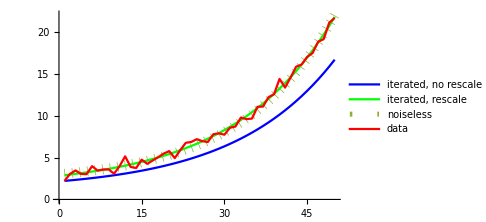

3.3228×10^-6

2.64092×10^-6

```mathematica
(***Diagnostic Tools***)

(*Parameter History*)
Grid[Take[debugParams,-10]];
Column[eFunc @@ #&/@ Take[debugParams,-10]];

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{
DataWith@iterParams,
DataN*Normalize@DataWith@iterParams,
DataWith@TrueParams,
DataN Data},
Joined->True,ImageSize->Medium,PlotStyle->{Blue,Green,{Dotted,Thickness[0.02]},Red},
PlotLegends->{"iterated, no rescale","iterated, rescale","noiseless","data"}]
eFunc@@TrueParams
eFunc@@iterParams
```

```mathematica
samt=50.;
smag=8.;
step=smag/samt;
smin=TrueParams[[1]]-0.5smag;
smax=TrueParams[[2]]+0.5smag;
SurfData=Table[Table[{x,y,#[x,y]},{x,smin,smax,step}],{y,smin,smax,step}]&;

Row[ListPlot3D[Flatten[SurfData@#,1],PlotRange->Automatic,ImageSize->Medium]&/@{SOF,NLS,HNLS,LS}]
```

-Graphics3D--Graphics3D--Graphics3D--Graphics3D-

```mathematica
InitialSearch=GridSearch[eFunc,20,40,10,{0.,0.}]
InitialSearch=First@GridSearch[eFunc,1,40,10,#]&/@InitialSearch
ItSearch=IterGridSearch[eFunc,20,20,10,0.8,5,{0,0}]
eFunc@@#&/@InitialSearch
eFunc@@#&/@ItSearch
Graphics@Point@InitialSearch
Graphics@Point@ItSearch
```

{{-3.,2.},{-3.,3.},{-2.,2.},{-2.,3.},{-3.,4.},{-2.,4.},{-3.,5.},{-2.,5.},{8.,5.},{8.,4.}}

{{-2.65,1.8},{-2.65,2.},{-2.65,1.8},{-2.65,2.},{-2.65,3.},{-2.65,3.},{-2.65,4.},{-2.65,4.},{8.,4.5},{8.,4.5}}

{{-2.64,1.84},{-2.64,1.76},{8.,4.48},{8.,4.56},{-2.64,1.84},{8.,4.48},{8.,4.56},{-2.64,1.76},{8.,5.6},{15.84,5.68}}

{0.00164067,0.00167115,0.00164067,0.00167115,0.00195335,0.00195335,0.00214719,0.00214719,0.00234304,0.00234304}

{0.0016437,0.00164151,0.00234304,0.00234313,0.0016437,0.00234304,0.00234313,0.00164151,0.00235856,0.00250787}

-Graphics-

-Graphics-

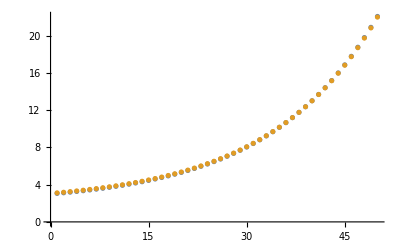

{2.8976,2.97545,3.0577,3.14459,3.23638,3.33335,3.43579,3.54401,3.65834,3.77912,3.90672,4.04151,4.18391,4.33434,4.49326,4.66115,4.83851,5.02588,5.22381,5.43292,5.65383,5.8872,6.13374,6.39418,6.66933,6.96,7.26706,7.59146,7.93416,8.29619,8.67865,9.08269,9.50953,9.96045,10.4368,10.9401,11.4717,12.0333,12.6266,13.2534,13.9156,14.6151,15.3541,16.1348,16.9595,17.8308,18.7513,19.7236,20.7508,21.836}

```mathematica
DataN Data - DataWith@TrueParams;
Norm@DataWith@TrueParams;
ListPlot@{(Norm@DataWith@TrueParams)*Normalize@DataWith@TrueParams,(Norm@DataWith@TrueParams)*Normalize@DataWith@iterParams}
```

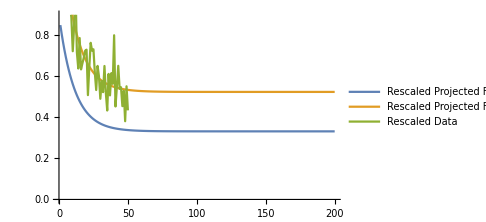
-Graphics-
Function as it is: 0.5+ⅇ^(-5. x)
Scaling Factor: 0.891118
Parameters in function as they are: 0.585518+ⅇ^(-4.50143 x)
Rescaled Function: 0.521765+0.891118 ⅇ^(-4.50143 x)

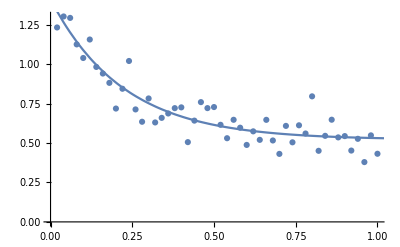

```mathematica
ProjectedRange=N@Range@(4DataLength)/(SamplingRate);
ScalingFactor=DataN/Norm@DataWith[iterParams,SamplingSet];
Column@{
ListPlot[{
DataN Normalize@DataWith[iterParams,ProjectedRange],
ScalingFactor DataWith[iterParams,ProjectedRange],
DataN Data
},
PlotLegends->{
"Rescaled Projected Fitting Normalized according to itself",
"Rescaled Projected Fitting Normalized according to the norm of the sampled range",
"Rescaled Data"
},
ImageSize->Medium,Joined->True
],
Row@{"Function as it is: ",Fitfunction@@Prepend[TrueParams,x]},
ToSpacedString@{"Scaling Factor:",ScalingFactor},
Row@{"Parameters in function as they are: ",Fitfunction@@Prepend[iterParams,x]},
Row@{"Rescaled Function: ",Expand[ScalingFactor Fitfunction@@Prepend[iterParams,x]]}
}
Show[ListPlot@MapIndexed[Flatten@{#2/DataLength,#1}&,DataN Data],Plot[Expand[ScalingFactor Fitfunction@@Prepend[iterParams,x]],{x,0,4DataLength/SamplingRate},PlotRange->All]]
```

```mathematica
Expand[ScalingFactor Fitfunction@@Prepend[iterParams,x]]
```

0.521765+0.891118 ⅇ^(-4.50143 x)